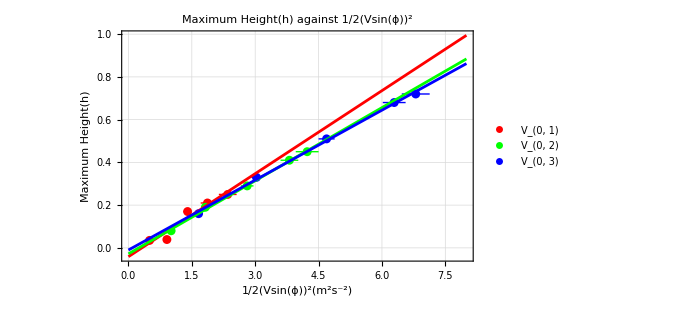
-Graphics-
V_(0, 1): y==0.129464 x-0.0412259
V_(0, 2): y==0.114019 x-0.0279573
V_(0, 3): y==0.109029 x-0.00997522

```mathematica
V1={{0.50,0.035},{0.91,0.039},{1.40,0.170},{1.87,0.210},{2.35,0.250}};
V2={{1.01,0.080},{1.82,0.190},{2.81,0.290},{3.81,0.410},{4.23,0.450}};
V3={{1.66,0.160},{3.03,0.330},{4.69,0.510},{6.29,0.680},{6.80,0.720}};

(*error bar*)
V1error={
{Around[0.50,0.03],Around[0.035,0.001]},{Around[0.91,0.06],Around[0.039,0.001]},
{Around[1.40,0.10],Around[0.170,0.001]},
{Around[1.87,0.16],Around[0.210,0.001]},
{Around[2.35,0.21],Around[0.250,0.001]}};
V2error={
{Around[1.01,0.05],Around[0.080,0.001]},
{Around[1.82,0.09],Around[0.190,0.001]},
{Around[2.81,0.15],Around[0.290,0.001]},
{Around[3.81,0.21],Around[0.410,0.001]},
{Around[4.23,0.27],Around[0.450,0.001]}};
V3error={
{Around[1.66,0.08],Around[0.160,0.001]},
{Around[3.03,0.12],Around[0.330,0.001]},
{Around[4.69,0.19],Around[0.510,0.001]},
{Around[6.29,0.27],Around[0.680,0.001]},
{Around[6.80,0.33],Around[0.720,0.001]}};

(*Extract x and y values for each set of data*)
x1=V1[[All,1]];
y1=V1[[All,2]];
x2=V2[[All,1]];
y2=V2[[All,2]];
x3=V3[[All,1]];
y3=V3[[All,2]];

(*Perform linear regression to find the best-fit lines*)
fit1=LinearModelFit[V1,x,x];
fit2=LinearModelFit[V2,x,x];
fit3=LinearModelFit[V3,x,x];

(*Extract equations as strings*)
eq1=ToString[TraditionalForm[y==fit1["BestFit"]]];
eq2=ToString[TraditionalForm[y==fit2["BestFit"]]];
eq3=ToString[TraditionalForm[y==fit3["BestFit"]]];

(*Display the equations outside the graph with extended line plot*)
Column[{Show[ListPlot[{V1error,V2error,V3error},PlotStyle->{Red,Green,Blue},PlotLegends->{"\!\(\*SubscriptBox[\(V\), \(0, 1\)]\)","\!\(\*SubscriptBox[\(V\), \(0, 2\)]\)","\!\(\*SubscriptBox[\(V\), \(0, 3\)]\)"}],Plot[{fit1[x],fit2[x],fit3[x]},{x,0,8},PlotStyle->{Red,Green,Blue}],Frame->True,FrameLabel->{"\!\(\*FractionBox[\(1\), \(2\)]\)(Vsin(ϕ)\!\(\*SuperscriptBox[\()\), \(2\)]\)(m^2s^-2)","Maximum Height(h)"},GridLines->Automatic,PlotLabel->"Maximum Height(h) against \!\(\*FractionBox[\(1\), \(2\)]\)(Vsin(ϕ)\!\(\*SuperscriptBox[\()\), \(2\)]\)",ImageSize->500,PlotRange->{{0,8},Automatic}],Column[{Row[{"\!\(\*SubscriptBox[\(V\), \(0, 1\)]\): ",eq1}],Row[{"\!\(\*SubscriptBox[\(V\), \(0, 2\)]\): ",eq2}],Row[{"\!\(\*SubscriptBox[\(V\), \(0, 3\)]\): ",eq3}]}]}]
```

```mathematica
G={0.129463677691274,0.1140194642341922,0.10902875373470124}
g=1/G
```

{0.129464,0.114019,0.109029}

{7.72417,8.77043,9.17189}